```mathematica
Solve[Q==(√(ω0^2-2 β^2))/(2β),β]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{β→-ω0/(√(2+4 Q^2))},{β→ω0/(√(2+4 Q^2))}}

5 √(2/163)

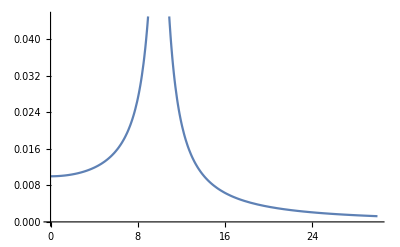

```mathematica
Q = 9;
F0 = 1;
m = 1;
ω0 = 10;
β = ω0/(√(2+4 Q^2))
Dv = F0/(m√((ω0^2-ω^2)^2+4 β^2 ω^2));
Plot[Dv, {ω, 0, 30}]
```